# Exercise Notebook for BProbeM (https://github.com/TSGut/BProbeM/wiki)

## Run this section to initialize the example matrix set. It will be saved to ‘InputMatrixList’.

```mathematica
firstM={{0,1/(√2),0,0,0,0},{1/(√2),0,1/(√2),0,0,0},{0,1/(√2),0,0,0,0},{0,0,0,0,1/2,0},{0,0,0,1/2,0,0},{0,0,0,0,0,0}};
secondM={{0,-ⅈ/(√2),0,0,0,0},{ⅈ/(√2),0,-ⅈ/(√2),0,0,0},{0,ⅈ/(√2),0,0,0,0},{0,0,0,0,0,1/2},{0,0,0,0,0,0},{0,0,0,1/2,0,0}};
thirdM={{1,0,0,0,0,0},{0,0,0,0,0,0},{0,0,-1,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,-ⅈ/2},{0,0,0,0,ⅈ/2,0}};
fourthM={{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,-ⅈ/2,0},{0,0,0,ⅈ/2,0,0},{0,0,0,0,0,0}};
fifthM={{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,-ⅈ/2},{0,0,0,0,0,0},{0,0,0,ⅈ/2,0,0}};
sixthM={{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,1/2},{0,0,0,0,1/2,0}};
InputMatrixList={firstM,secondM,thirdM,fourthM,fifthM,sixthM};
```

## Initialize the package and do some routine consistency checks

```mathematica
<<BProbeM` (* load the package BProbe *)
```

Loaded BProbeM. See the wiki () for documentation and help.

```mathematica
Length[InputMatrixList] (* check how many matrices / dimensions we are working with *)
```

6

## Testing and scanning

### Try narrowing the problem down to subspaces. Subspace→ {1,2,6} shows something interesting when using the Dirac operator.

```mathematica
ProbeInit[InputMatrixList,Probe-> "Dirac",Subspace-> {1,2,6},StartingPoint-> {0,0,0}]
```

Energy Probe | Dirac
Starting Point (SP) | (0
0
0)
Energy at SP | 0.00000000000000000358958
Norm of Gradient at SP | 0.000000000000248974
Absolute Hessian Eigenvalues at SP | (0.0799519
0.0799519
0.0799519)
Local brane dimension at SP | 3
Dimension of Target Space | 3
Dimension of Hilbert Space | 48
Step size guess | 0.110064

### Try testing the waters with a directional scan. Remember that the directional scan only scans the directions you specified in the subspace option, so if you want the most complete directional scan you should perform it after initializing on the full set. You should try a few different step sizes for the directional scan. Think of this like manually focusing a camera.

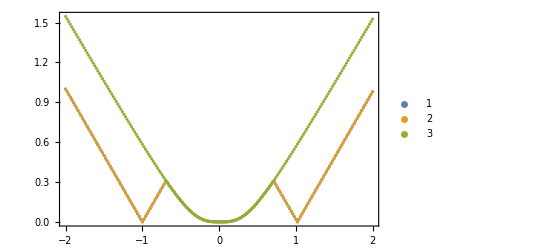

```mathematica
ProbeDirectionalScan[0.02]
```

### The Dirac operator shows two clear minima, so we need to be careful when scanning. If we scan carelessly we will only scan one of the two minima and lose information. A good approach here is to set the starting points inside of the local minima region and choose a small step size, i.e. scan the two local minima separately and later combine the two point clouds.

### Let’s start with the internal structure:

```mathematica
ProbeScan[Dimension-> 3,StepSize->0.1]
```

Number of total points gathered | 1858
Number of points currently processing | 0Status Information

```mathematica
ListPointPlot3D[ProbeGetPoints[], BoxRatios->Automatic] (* Plot the point cloud of a 3D subspace *)
```

-Graphics3D-

```mathematica
ProbeReset[] (* Use this to reset the point cloud data to switch to a different step size! Careful, save your pointcloud first if you don't want to re-compute it! *)
```

### Let’s save the point cloud for the internal structure:

```mathematica
pc1=ProbeGetPoints[];
```

### Now for the external structure. We manually place the starting point into the approximate area of the other minimum. To do this we look at the directional scans. They tell us for example that the second local minimum area contains the point {0,1,0} on the Subspace→ {1,2,6}. Thus, this is one of the many points we could use as our starting point to scan the external structure!

```mathematica
ProbeInit[InputMatrixList,Probe-> "Dirac",Subspace-> {1,2,6},StartingPoint-> {0,1,0}]
```

Energy Probe | Dirac
Starting Point (SP) | (0
1
0)
Energy at SP | 0.0000000000000000168517
Norm of Gradient at SP | 0.00000000000315412
Absolute Hessian Eigenvalues at SP | (0.9999
100.
100.)
Local brane dimension at SP | 0
Dimension of Target Space | 3
Dimension of Hilbert Space | 48
Step size guess | 0.110064

```mathematica
ProbeScan[Dimension-> 3,StepSize->0.02]
```

Number of total points gathered | 315
Number of points currently processing | 0Status Information

```mathematica
ListPointPlot3D[ProbeGetPoints[], BoxRatios->Automatic] (* Plot the point cloud of a 3D subspace *)
```

-Graphics3D-

```mathematica
ProbeReset[] (* Use this to reset the point cloud data to switch to a different step size! Careful, save your pointcloud first if you don't want to re-compute it! *)
```

### Let’s save the point cloud for the external structure:

```mathematica
pc2=ProbeGetPoints[];
```

### You should have found this structure on the inside using the Dirac operator and Subspace→ {1,2,6}. The step size used here was 0.02. That’s a small step size, your initial scans should not “commit” to so much computation time until you know what you are doing will lead to interesting results. You should test the waters with more coarse step sizes first, such as shown in the second picture (step size used on the second picture was 0.1).

```mathematica
-Graphics3D-
-Graphics3D-
```

### You should have found this structure on the outside using the Dirac operator and Subspace→ {1,2,6}: -Graphics3D--Graphics3D-

### Combined point clouds using the Dirac operator and Subspace→ {1,2,6}. You can combine two such saved point clouds by simply executing ListPointPlot3D[{pc1,pc2}, BoxRatios→Automatic]. In high precision it would look like this: -Graphics3D- Let’s look at the combined pointc cloud for another subspace! Here is Subspace→ {1,2,3}:

```mathematica
(* Combined *)-Graphics3D-
(*only internal structure*)-Graphics3D-
```

### In principle we can (and you should!) do this for all subspace options. You can also scan the whole space but then you need to manually plot projections since you won’t be able to plot the 6 dimensional points. A good bonus exercise: Try “cutting” into the point cloud to see if the “bubbles” seen in Subspace→ {1,2,6} of the internal structure are hollow - they are!

## The solution: The matrix set contains something like a fuzzy 2-sphere and something like squashed CP2. The two geometries were manually combined to create this exercise matrix set.

### For some more information on those two matrix geometries individually, see the paper introducing the original BProbe: https://arxiv.org/abs/1601.08007